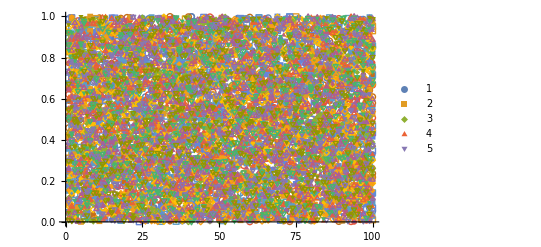

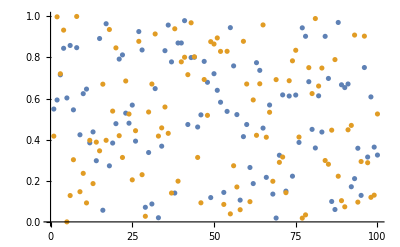

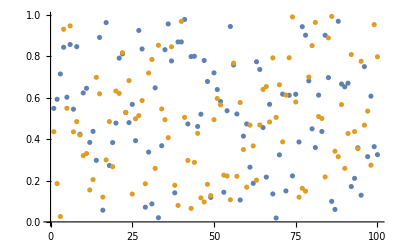

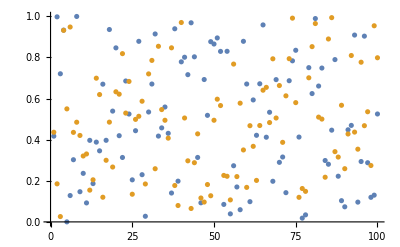

```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/ran_check","Table"];
n:=Length[codbar]
codbar12={codbar[[1]],codbar[[2]]};
codbar13={codbar[[1]],codbar[[3]]};
codbar23={codbar[[2]],codbar[[3]]};

ListPlot[codbar,PlotLegends->{"1","2", "3","4","5"},PlotMarkers->{Automatic,6}]
ListPlot[codbar12]
ListPlot[codbar13]
ListPlot[codbar23]
```

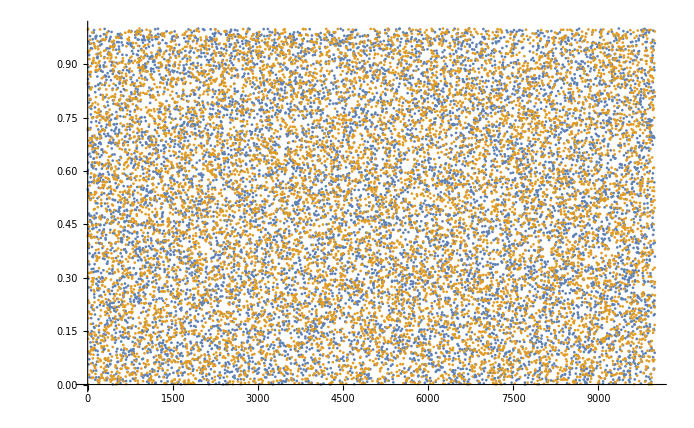

```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/ran_check","Table"];
n:=Length[codbar]
codbar12={codbar[[1]],codbar[[2]]};
ListPlot[codbar12]
```

```mathematica
x1x2=Total[Table[codbar[[1]][[i]]*codbar[[2]][[i]],{i,n}]]/n;
x1x1=Total[Table[codbar[[1]][[i]]*codbar[[1]][[i]],{i,n}]]/n;
x2x2=Total[Table[codbar[[2]][[i]]*codbar[[2]][[i]],{i,n}]]/n;
x1=Total[Table[codbar[[1]][[i]],{i,n}]]/n;
x2=Total[Table[codbar[[2]][[i]],{i,n}]]/n;
x1x2
x1*x1
x2*x2
x1x2-x1*x1
```

0.257407

0.278868

0.240811

-0.0214615

```mathematica
x1x2
x1x1
x2x2
```

25.7407

35.0364

32.9613